```mathematica
""<>ToUpperCase[#]<>""&/@Import["https://en.wikipedia.org/wiki/Proteinogenic_amino_acid","Data"][[1,1]][[4]][[2;;]][[All,3]]
```

{ALA,CYS,ASP,GLU,PHE,GLY,HIS,ILE,LYS,LEU,MET,ASN,PYL,PRO,GLN,ARG,SER,THR,SEC,VAL,TRP,TYR}

```mathematica
Import["https://en.wikipedia.org/wiki/Proteinogenic_amino_acid","Data"][[1,1]][[4]][[2;;]][[All,3]]//Length
```

22

## Download training set

```mathematica
cullPDB`list="/Volumes/WDBlue/!Advanced_Machine_Learning/Final_project/training_3/cullpdb_pc25.0_res0.0-2.0_noBrks_len40-10000_R0.3_Xray+EM_d2022_04_25_chains6968"
```

/Volumes/WDBlue/!Advanced_Machine_Learning/Final_project/training_3/cullpdb_pc25.0_res0.0-2.0_noBrks_len40-10000_R0.3_Xray+EM_d2022_04_25_chains6968

```mathematica
cullPDB=StringTake[#,4]&/@Import[cullPDB`list][[2;;,1]];
(*Print@OutputForm@StringRiffle[cullPDB,","];*)
Print@OutputForm["["<>StringRiffle[("'"<>ToLowerCase[#]<>"'"&/@cullPDB),","]<>"]"]
```

['5d8v','3nir','5nw3','1ucs','3x2m','2vb1','1us0','6e6o','6s2m','1r6j','4rek','4i8h','2wfi','2ov0','2b97','3x34','7kr0','6l27','5yce','1gci','7a5m','5gv8','6zm8','1x6z','4ua6','5tda','7af2','3ui4','5al6','5nfm','1w0n','5hb7','2h5c','2vxn','1nwz','7avk','2jfr','2o9s','6tgu','1p9g','7bnh','2ykz','4eic','6eio','2hs1','4pss','4ayo','6q00','6q00','3o4p','6etl','1mc2','1x8q','7bbx','7aot','3qpa','5emb','2fma','5xvt','2f01','1g6x','3wdn','1muw','3zsj','6zpa','2ddx','1v6p','4hs1','5l87','5o99','1gwe','3zoj','3fil','4f1v','5lp9','1i1w','4u9h','4u9h','6kfn','4o6u','3ip0','4wee','4y9v','1g66','1ix9','6klz','6fmc','4npd','1vyr','5x9l','7psy','1oew','3vor','3g21','5gji','3zr8','4nsv','6xvm','2xu3','6lk1','1j0p','2pvb','5a71','5ig6','3g46','5br4','3x0i','7p1q','5mk9','4hno','1iqz','6eqe','3ea6','6hsa','2fvy','4g78','6cnw','1l9l','3wgx','6zsy','1ok0','6ri6','1vbw','3ql9','3m5q','1kwf','2bt9','3qr7','2uu8','2gud','4mzc','4a02','2xom','2xjp','7asq','5u3a','7a3h','1mj5','4wka','5zgx','4kqp','5o2x','3s6e','4xdx','3dk9','1zzk','3vla','4g9s','4g9s','4e3y','5ewo','3dha','6j93','1rtq','3ned','7dc4','4egu','1nki','3f1l','4ga2','6iip','1ufy','3zzp','1k5c','3puc','5dp2','3agn','5jug','2xod','2e4t','3kff','6jpt','3e4g','4r5r','1aho','1u2h','5a8c','1xg0','1xg0','2xfr','1byi','4acj','6x7j','7rwg','5dze','5tif','3eo6','1zuu','4q4g','3vii','1m1q','4oo4','7l71','3goe','1xmk','4mtu','6yp6','6fjn','3aks','3v1a','2v8t','4hgu','3d1p','5sy4','3ju4','1ixh','3psm','4wpk','4a7u','2pne','1unq','1k4i','1tqg','5sbq','4iau','1mwq','3q46','5ckl','2fwh','5o45','7kom','6rk0','4aqo','6rvu','6g1i','4gzn','6u66','5ii8','4rj2','7log','7b1s','7b1s','7b1s','4nds','4x5p','5jdk','6yk4','2gkg','7adr','7adr','1jfb','7adr','2cws','1eb6','3aj4','1o7j','3fym','4n1i','4bj0','6pws','1lni','6igg','4zgf','5ws7','1gkm','2r31','2ggc','1tt8','1q6z','2rbk','5idb','4ymy','2jhf','3noq','4gnr','5ctm','2a6z','1od3','3rwn','5sv5','1mn8','6gz8','3l8w','2vha','4axo','2x46','6fvi','2p5k','5d66','2ce2','3rq9','7k9c','1oai','4jp6','6i3b','1c7k','6ukf','1zk4','3a4r','3soj','4txr','4txr','3jyo','6l8g','3bwh','3a02','2v1m','3ccd','7b5w','3zuc','4ypo','3teu','3sk2','7jja','4bpf','4za9','6z5y','3nbc','5jh8','6y4e','6qaz','1i27','5mdu','1cc8','6i03','5aot','3nvs','5yde','7rm7','7niy','1kqp','4uhc','5m17','4wx4','6ef7','4uyt','4udx','3b64','3o1n','6q3p','6q3p','3rof','1y93','4xpx','1xqo','5d5y','5onk','3vz9','3vz9','6dcm','3qzr','6n9h','3a72','2ob3','4rv5','5fbf','5tnv','6fm7','5ima','3i94','5ae0','2heu','5p9v','6mm2','2r16','3cuz','1i2t','4b9g','1d5t','6s07','6bev','3c70','1lwb','6ry0','1psr','6f9o','1yqs','3eun','4co8','6tve','2oiz','7e2s','5nwp','2oiz','7d8d','2v3i','6nnr','3fs9','1fsg','5fi3','2c71','2xwv','7mpd','3gmx','4mnc','4yaa','2vzp','5b8d','3iqu','6sid','2x5y','4w7l','3r2q','5faf','5ctv','5qi0','3wmv','3vup','4ann','1m2d','6wqy','3pb6','4w7w','1euw','1jcl','2vzc','6c1x','6tcc','6elv','3r87','7esk','2axw','7lkl','7lkl','1m9z','2hin','5u4h','6r4z','7et5','6h40','7tfm','4d8b','6b8f','4xot','3tc8','6hav','4fk9','3ulj','4kgd','3w42','3mcw','1n40','3nyc','6yoo','7biu','2dko','2dko','2r0x','7cka','7blk','3lb2','5hub','1pmh','1sfs','6gx2','5tfq','3cij','3vgi','2w72','2o90','4qrn','5olr','6v67','6s5w','6s6c','6wfn','7cx5','4q2l','4k12','4k12','1jbe','2ci1','6tm3','1w23','1w66','4m51','6p2l','2xw6','3wa2','2yhg','1ds1','6se1','4mq3','4l57','5oj5','6ekz','5lun','7o4p','4bps','5opf','6xy7','6gy5','4g9e','2car','1nkd','6tho','6zeg','6fiy','4wui','4zo2','1qlw','1n62','1n62','1n62','5y9z','5j1n','3t7l','6uo3','6ftf','5ohq','4rxv','1c5e','1zl0','3rpe','4cj0','5z3e','6t85','5el9','2z72','4wwf','3lwx','4a9v','6rrv','7nqg','6rz0','2aib','4a29','3ro3','2v9v','2osx','6r1d','4he6','2v89','4ate','2nwf','5jbx','3qzb','7lv6','2c2u','3e8m','1gmx','4qlp','4qlp','4wpg','3kwe','4lf0','1sby','1z2u','4h7w','1t8k','6g7n','4jz5','6mu0','4cvr','3p4h','7o91','4mak','4j8c','2w39','2nxv','4m91','4mij','3rzn','2vfr','1f86','6w2g','3v0d','1bkr','1t2d','6e1z','4xuw','6exx','7qf3','1uz3','2fba','2v8f','3ct6','1rg8','6dyf','3nzn','3su6','1yfq','3bvx','4cd5','3od3','4pf3','2i5v','4etn','4b1m','5ljp','4cng','3mvs','4bt7','4qa8','3lqb','5nkg','5d7w','2rhf','3mre','6yv5','6t02','1kt6','2ii2','3bf7','5m1p','3tg2','5iwh','5vny','3u97','6bxd','6h10','6dqh','1oc7','4mf5','2ofc','3oru','6tl7','3a8g','3a8g','5wsf','5ouo','5w0h','3ci3','4yap','6osh','3g5t','5jvi','1sau','1k7c','6pzd','4hcj','5n3j','5mx9','5emi','3u01','6rg2','1tuk','6f4q','4ck4','6e7e','5ufy','4i4o','2wj5','4yec','4yec','6ght','6syv','1ra0','6luj','2eab','6t92','3ds4','3tys','7baf','4knk','4zur','5gtq','6hph','6zc2','1u07','4bpz','6n4l','3d9x','6swi','7dqt','5lzg','6q9l','4jcc','6rvq','1p6o','5aoz','2j45','5um2','5ue1','4bk7','6elm','4w8h','5nb4','4qpw','4inw','5kla','6jv0','7a73','3s2r','6znv','5kar','6hfq','5uqz','2zk9','7cn7','4jxr','1tkj','4yz0','3dlc','4uu3','4wn5','2oln','4n03','1hdo','6np3','6h8o','4h3u','1gwm','6t9q','3zzo','6cwm','3w06','2nsz','4jn7','3dnj','4ezi','4ku0','4ku0','4dt5','4zvf','6k7c','4jk8','3m73','1odm','7ldq','4u98','6geh','4jiu','2zpt','2r01','1xmt','2ciw','1i4u','6uaq','3r72','5t38','3s0a','2ic6','5g38','6nlq','7mqq','4beu','4hro','3t3l','2ylb','5bty','5k34','3bfo','2dkj','1k8u','2fhz','2fhz','2o9u','6cpb','5aig','5ls7','7p50','4al0','5z0d','6c4q','1h4x','6e1f','6q43','6q43','6q43','1x9i','6l7q','2vh3','6tn5','5few','5a6m','7lwe','4ue0','1h97','4rjz','3x0t','6b1k','6sj3','6enn','4emn','5ykz','1wkq','4ru3','5w8q','5o15','4nno','4bfo','5tzm','5f6r','6ssd','3wdc','1kq6','5zhz','7bxd','6mrr','6t6h','4jht','5v6j','6r01','5q22','5uq6','5dic','3a5f','4yep','3s6f','1uwk','4rlz','5lw3','3ujc','5h7t','1gu2','6lxu','5j41','6dga','2xio','4lld','6s95','6fsn','2fj8','5szc','6iux','6etc','6x1x','5uuk','1sen','7nza','4od6','2bk9','5e9p','1h12','6sao','2nlr','5jry','6i6m','2v3g','3ir4','3hyn','4pq9','1vr7','6gd6','4rgd','6zpv','4igi','2iay','4yi8','6sll','5mfa','5hhj','7at0','6bo0','3bwz','2bhz','1c0p','1m15','4zju','5by5','1knm','5l4l','1j98','3b4u','3m0z','1xdn','4d0q','3ohe','5ah1','2h1v','3h5j','4l8a','3gne','6ufe','6xfj','4nog','3vqj','2icc','3ipj','5cwg','3sqz','7k3t','4uas','2gxq','3edo','6spo','5e0j','5oxz','4ebg','6pqk','3og2','4wwh','2x5x','4n6k','5wqj','4nyh','6d9n','1ucr','5k2l','7ehu','5kb6','2fcl','6cbu','4p40','6a56','3bzy','2qf4','6i9a','6su5','4nyq','5v2o','4fr9','4lup','6et6','3oxp','3tg0','6t0y','6kfs','5gjh','2pgn','2znr','7jgu','6fu9','6fu9','4uqx','1w6s','7ezi','1w6s','2dlb','6z4n','6dt3','2r2z','2bmo','2bmo','2zex','5toq','6q0m','6qxr','3buu','4gwb','5igi','6hbb','1nz0','4iiy','1tu9','4o0a','4bgc','1vk1','6uof','5mr1','4el4','2w5q','3a6r','1x6i','4gmu','1qw9','5cph','7avc','4rfu','7eyl','2a26','3n17','3b12','3qvp','2vk2','2h8e','1z2n','3dqy','3r9f','6qxu','2cg7','1i24','1wn2','1o7i','3g36','6ita','4zy9','1v8h','1ryo','1jet','3sg0','7du7','1q6o','4hi8','4hi8','4wjt','6l0o','4yki','7bj9','4oxx','6ih0','1d4o','3bmz','6sqp','3b5m','2wnp','6ut9','7chr','5ggn','5x5m','6i05','5i90','4r6y','3m7a','5m10','6jlv','6i4e','3oqp','6gvd','5x7l','7etk','1kyf','3d5y','3c8l','6yx3','4x7g','5hob','6kbx','5vx1','2y0o','2v9l','1w7c','2a3n','3g91','6hhm','6y01','4dqj','4zx2','3f7e','3h4x','6jwm','6y56','5r8q','6l1p','4d6g','3f7x','3qu5','5l77','4jl5','7ee5','5c17','4pj2','6ggc','2bji','4e3x','6q1m','4x9t','2w1j','4a56','4f0w','1usc','4q8m','7ek6','4xez','5c5g','4hy4','5j4u','5xbc','6utc','5lxx','1m4l','3ppl','3mqd','1rwh','6e85','4s28','3giu','4ps6','3mmh','4j5r','1e58','5m5z','5dvi','4rwu','7miw','4qpn','6qhj','2r6v','4pz0','1gnl','3see','3oyv','3u9w','6srh','4jgl','3grd','4muv','3amr','2gb4','4x84','5uwz','3qzm','3njn','7br1','6x7h','4upi','5ihw','6yb7','7qu5','7s3w','2hba','3k67','1s3c','2yh5','4k0n','1eaq','2w8t','4fn7','3r6d','5nj9','5nj9','2cov','3sgg','7txs','7esw','3n08','3zrx','6pvj','2wlv','2p2s','3qoo','5y1f','6x84','4afm','4noa','3b0g','5jj2','6gbi','6dop','4c6a','2wwe','3up3','5ewu','6ubd','6kxt','7evc','6r2w','6r2w','7e04','4qas','2qjz','3ak8','3ivv','6tak','3f9x','1qft','1y6x','7da0','7da0','2g3r','1oaa','2gom','3o2r','5d78','4pkl','6e4d','4to7','7fds','7c6c','3pd7','5noa','4qp5','3ur8','4f98','5gng','3s4e','6tab','2fcw','3zn4','3wk3','3nhe','4j4z','7kbg','4l4e','4chi','7q4t','5gsm','5aog','5vhg','4xqc','4q53','6i1a','5ik4','5bmn','3f40','5dhd','2cc6','6avx','7s5h','5nsa','6h17','3w19','4r75','5ulb','5ol4','5ol4','5ol4','4lyp','4rz9','4uul','7oyw','6ix1','5u69','4mjd','5m33','4ohj','2y7e','7kpo','4yud','6hqc','5hj9','4ep4','5n8a','3tvj','4exk','5kvs','5h9n','4j42','3tm8','4euo','2pc1','3rkg','4ltt','1t1i','5ly8','4hcs','6ts3','1qks','3meu','6r09','1rtt','4ruw','6at0','6qps','5eyn','4wdc','2z26','4v2k','3mu7','6jz2','6sa5','4tkc','7omv','5o6h','3m9q','6st4','4fzp','7w83','2xn6','5yvk','7os5','6fc0','3pqh','6j33','6hur','3s2j','4qek','6qo9','6ne2','5x2e','6vrd','6ll8','4wbj','3t2c','6er4','4w9z','4s39','5zw7','5uej','4q5k','3myx','4q98','4m1x','5a0n','3g0k','3hwu','4iil','4f06','6xtd','6xtd','4jg2','5v01','4z39','3znv','6gcv','4zhb','7obv','7obv','4rle','3fgv','1g61','2nqw','3drf','5inb','1ka1','6rs4','1fcy','3ogn','3nbm','4gvq','1xub','3l9a','3c2u','4brc','1vly','3kkf','7lqx','4p7x','2prv','4xfk','6ulo','4cfi','2okt','3hm4','6trj','2vla','4bn4','7jzs','3eur','3u7z','3ebt','4pvk','5oby','1lq9','7rg8','5gqi','3e8t','2ccv','7rg8','6ff1','3wdq','6stl','1nxm','6fmb','1wvf','4h27','3wuz','6n1b','2xki','1gk9','5nrh','5mu9','1gk9','4qc6','2qsb','1jcd','7coh','7coh','3mqz','7ani','7coh','6vh6','7coh','7coh','7coh','7coh','7coh','7coh','3b9w','7l7x','2v6k','5hb6','5b4z','2x9z','2xhf','3uff','4gmq','3lhs','3ga4','1mjn','3f2z','1sg4','6t2t','1nuy','5ok6','2mhr','1t6u','2y5p','6b29','1tbf','4jbd','6jwf','5mfo','3pn3','1kmt','4gxw','2j6b','7o39','6jsa','5cwh','2nr7','3pmo','3epw','3hlx','4fch','3da8','4kem','2izx','6hxm','2r5o','4rd4','3qu3','1cy5','5exh','2gf3','7f82','5zry','3s8s','3ndh','7dhp','4qbo','2gso','3no0','4lgt','3cim','6w92','4h8e','5yh4','4cgs','3d3b','3n01','3d3b','2nlv','3b34','7kjg','3bqp','2imq','6fdg','6tgk','3b0t','4p82','2d1s','1hyo','1yg9','7s7y','2imf','6kjk','4ac1','3l1n','2d5w','1wcw','7nsz','5io9','5trq','2gqt','3g7n','7oxd','6l5h','5z42','1es9','6lac','2fcj','5y4z','6tg6','1zce','2ecu','1hdh','1ucd','2grr','2j9w','2gec','2pv2','2pxx','7bqi','4gzc','3jtz','1uso','1vd6','2ehp','5dzo','3t47','4nqg','6t6e','5ol9','6bsc','6bsc','5ehi','5zt3','5l0v','6nsv','6jv7','2xqq','4uob','6tto','3bln','5bow','5sv2','7vjo','1vmh','3acx','4yuc','2rdq','2vc8','4nbp','6n6j','7fh8','1gxm','1e7l','6gg7','7thh','6gg7','4gc3','5hdk','5xdh','4eae','6tj2','2ibl','3gbw','5hqh','1mkk','4edh','3cm3','6d4k','5b08','4in0','6z96','7cdy','2xts','2xts','4hms','3lhi','6riv','5jgk','2y88','4pmo','5m2p','6z1v','6i5o','1kko','6os6','2uv4','5yvn','3ngg','4efp','6jjt','4ee6','6van','5m97','7chq','6at4','5jed','6ajp','5wk0','7r84','5opz','5ktn','6ydr','5ej8','5viq','3qxc','6ctz','7b3a','4phr','4bgb','3tow','4cp6','3suk','7kzw','5yhr','6ds9','1vh5','3q4o','7ef6','6z2t','1utg','5w7w','4q29','4cw4','4cs4','3wx7','3pfg','6f3p','4qhw','4rk5','3pe6','5cof','4zh5','6sbc','2qe8','6sj8','2yfo','6e1x','5mh6','5umh','3oq2','6b6u','5a7v','5a95','4r3n','5a0l','4kdw','3wiw','6m9y','5ujc','6pyk','6edv','2ovg','3gfa','3ocu','2yny','2z51','6z68','5hwa','6f43','4whs','3rx9','3i4g','2gke','6fc1','4h6c','2iyv','1oh4','3s9x','3wg3','4ix3','6sun','2zhj','6two','5vn4','2jda','3no2','6zrw','5tkw','5tzp','5oq3','6hni','5omt','1lk2','3bc9','3ib5','3i10','6tcb','2xol','4esm','2gkp','3g6k','6uqv','4jf8','1g2r','3k01','4rxt','6dcj','5isv','4mno','3u6g','1wdd','3ckm','4ak2','6tyk','1vkk','4di9','4ndo','4dt4','1fd3','3sbm','5eha','4g0x','2xdw','2phn','5i45','2ehz','6tzn','6xya','4dp1','4gvf','2e5f','6h8g','6zzj','4reo','4pe3','4ruq','4eqp','5feb','6g6k','3sjm','2z5w','4yx1','1r6d','1wzd','6gaj','2i49','6f8a','2wy4','1e5k','2qjw','2wds','2hal','6gi4','6f5z','6p28','4q2s','1pz4','2eiy','3bm7','4h4d','4rpt','2vov','7p6s','3szy','1ukf','6udv','2ip6','1yn3','3bux','2hd9','5mao','5vw4','5n41','4ipu','6c74','4h6q','4x1z','4az6','6nd7','2akz','6qpk','5cec','5vfb','4rp3','3i45','6tc2','7nmq','3b0x','6tyy','5ko5','6wes','5l74','6z4w','4h5i','6e28','5yqw','6hiu','4dm7','6zco','4muq','6hgm','4lpq','4hwv','4iyj','5z0u','1jo0','6ksr','5o37','6pcd','6h5w','6uuy','1ouw','3so6','3b79','6nio','4cfq','7s5a','7ms0','6es9','6e5f','3cjs','7e4v','5muj','3c3y','5htl','4myd','6ry3','4boj','5o29','5mjr','4bqn','3ub6','7bx9','5cl8','7jp2','4x00','4psr','6r5j','6ysp','6y4j','6ldl','4i6r','3g7r','4hwm','7qbp','5xtu','1gve','5zdm','4xzf','2jek','3fz4','3nuf','5yqa','7k5l','3v4k','5wl1','6w0v','6w0v','5wfb','4eyz','5hgz','4wzx','5wwd','5m0w','5y9x','5qiv','3c8y','5yku','6xzl','5ufn','6sre','6vvn','3vk5','2vws','4oa3','3cp7','1n8v','2nuh','2we5','2c3v','7a03','4zhw','5j90','3zvs','4y2f','7d55','3urr','6c30','6dnm','4x9r','5wmk','6k39','5z8a','5xc5','7nlc','5j1s','5j1s','4avs','5emx','5hgj','6myd','4zav','2c5a','5t3b','6fop','1wb4','5a12','6w6b','3e4v','2bkx','5u81','6ytz','1qnr','5b5l','4ydp','4lhs','2w91','4c5k','3e8o','3a09','4jm1','3lg3','1q7l','6ewm','1q7l','7ost','2qpx','2odk','3k5j','4ry1','1u7g','5wkr','2w7a','4wy4','4wy4','4wy4','2g7s','3gzr','4n02','4leb','5thk','6gqz','2gyq','7e7f','4il7','5w2f','5ta0','4wck','4do4','2p51','4tvv','4b6g','3ejv','6wl5','2ozh','3iqt','5f4c','6sld','6rcg','5wfy','7aky','2p8i','7c1u','4ytb','5xbi','3a8u','1u7i','6er1','3v75','4pqh','7aah','1gk8','4guc','2ftr','7mjw','4qtc','3cwn','4q4w','4q4w','4q4w','3isx','3wva','4opc','6zxq','6oc0','6wgm','6coj','6coj','5ewy','6pt8','5vgl','3iis','3go5','4zbo','3llu','7plp','7fe4','5frd','2fsq','2fi1','5ixh','4lxq','6z6e','1ezg','6r7v','4x7y','6e3a','1q5y','4l0n','6t8i','3ach','3plw','2ra9','6ewl','6g8y','3m6z','3dqp','2qng','3ult','6ba9','3boe','6nzs','4qhq','3hzp','2hox','4eq9','5edf','2vs0','3ls9','6xru','6xru','3ix3','5lal','2oxg','5nt7','1zi8','1eaz','2cxn','5cr4','3kyj','5xvj','2cb8','3b0f','6m76','4i3g','2hzl','3u3g','4cv7','4kqi','7eam','6chx','4wri','6t84','7jjk','5anp','3d4e','3km5','4r1j','2gqw','3u65','3h0o','4qi3','3hf5','3mdu','5nrm','2oct','6u4z','6rra','3oaj','1s2o','3kkg','5j4f','1c1x','4ye7','7b0e','1rl0','7al1','4r9f','1y8a','5jaz','7s56','2qfa','2qfa','6x6z','7p8x','3g1p','3b8z','2vng','6yld','3plu','1ew4','1g5a','4rpm','2wag','1jf3','3aia','6a02','5i0y','5ml3','6sqk','6h20','4alz','2w3g','1k7j','2g7o','1n13','4fp5','1n13','1yge','1r6x','1y43','3m8j','3no7','4zc3','2ew0','2tnf','7mq3','2xz2','3fke','1nyc','1g8a','5h3v','4e2x','2f1s','2fq3','1gp0','1ng6','3qfs','1es5','2ddr','2e1h','1g6c','1ifr','1v30','5jo8','2e3p','4ytw','4ytw','3zzy','3bqx','2pof','2gu9','1s0p','3uxj','5zho','4zv0','5flw','5jda','6a5d','6xxj','2f5v','7z2t','5v8s','3fde','4luk','5hee','2p0n','6tjq','6gn5','7f22','6ro6','2f46','1xsz','6o5w','5de3','6git','5i5n','7ld9','7ld9','7esr','2wq4','3mao','6wm6','6fpq','4ler','6f4j','7n7h','2f22','1mxr','7bjt','6pnv','7mpr','6fz6','7m1a','6rwt','4m7x','3lhn','6fyr','2ozt','6xl7','2vk8','1pkh','2pqx','6x7n','6b9x','6b9x','6b9x','1pp0','5v1y','5ep2','3a35','5a10','6ndt','5ht2','4pux','5yj6','7ofv','6shu','6tjr','7ody','6bcd','1m7g','1rk6','1v05','2opc','6yip','7cly','5lus','4n2p','6jqw','5vsn','5jw8','5ykr','5ncb','4up3','6yii','4e4r','5m0n','3lmz','6qvf','3gzb','4ld1','3bje','2cjt','3ftd','7kd7','4ph2','3vg7','2qjl','3zxk','2ia7','6teq','2pr7','5n0o','6rxa','7dry','7dma','7dma','3mbr','7ndy','5r7x','6pcz','4g7x','4g7x','4ypc','6dg4','4max','4jnu','7vw0','7cq3','5gt5','6n9m','4nxy','6ac0','3o9z','6vig','4s1p','4b4u','4l9p','6nmo','6qsp','5swc','5eqv','5uam','4evu','6xm7','1e6u','4z04','5eo6','2hw2','4hc5','2ckk','7ao3','3jum','3h0n','3zoq','6tr4','6pt4','6amg','6i3q','4z47','3e0x','3led','6hxp','3wli','3gr3','5jbn','4hls','6ofq','3f6y','6q1h','3mwx','4htg','6y65','5vps','7lda','3g16','3hx8','2fgq','4ufq','4q7o','5l20','7q02','1rcq','4l2i','4l2i','2nn5','3ke7','3imk','2j1v','6z0m','5fvn','6ibe','1wl8','6ywn','3giw','1w1h','3d5p','6tfr','6xb6','7npp','3bed','3qc0','4au1','4ium','2end','5coz','3uue','3fcn','6fxd','4og4','4icv','1qqf','2f5t','3kwr','3u2u','2xs7','6bd0','5lt5','3lyd','5kvb','2vw8','4pp4','6ull','7b67','2hew','1x54','6hto','5dcy','2vez','3itf','6m64','4z3g','3wur','6uid','7ms7','6xoj','6r0r','3f14','7o8f','2glz','5hoe','4p3h','4i6y','2odi','6s2r','2wlr','1xd3','7r65','4v4m','2x3m','3ors','4dri','3m0m','7k44','3ga3','5nhu','3r5t','1xbi','2erf','2b0a','3s44','2qfe','1wlu','1bgf','2wol','1hz4','5c5z','5g51','5d3u','1hzt','3eye','4r78','3tew','1xlq','1w5r','1is3','4iej','7jid','1idp','1n7s','1io0','1c1k','4b21','1wvq','1v4p','3d7j','1xyi','2egv','4oq9','2rl8','3by8','2gxg','1xaw','3poj','5ep6','3t94','6j6l','4z9h','3lae','3rtl','6hk9','6c9x','4zqx','6tbi','2fb6','7sf6','4l2h','6vyd','2j5g','4fzl','3i7m','5a8j','2oh1','5hhe','1fx2','1tke','5mgw','6hcw','1lc5','3mjv','4ysl','3sy1','6sxt','7kih','6fth','5ls4','3mjf','2hzc','5tpi','6gpk','3n4j','6cng','5ky2','3gjy','1ju2','6ae9','3n3m','3wkg','4boq','4cd8','3fg9','6cuk','7bvt','3hpc','4mth','1rku','4xxl','5ysq','6p8j','5agi','7lvm','3p0k','1r7j','6zm0','4ocv','4mam','4mzj','4eu9','4pw0','4jbb','4hnl','1gqi','5js4','4dwr','2q3w','2c15','3vsv','7oec','4ftf','4v33','6z1k','6evn','5o1l','2fr5','4cay','6ykf','3dsb','6fig','2dt8','2bcm','3rob','2z8x','6tqd','3zja','1b67','3vmk','4hly','3c9u','1wpu','5tvo','5xj5','5hml','4wqk','3l46','6zrn','5o75','5n86','5d6e','3mc3','4nzk','5ynx','3mcx','2w1v','7rea','7dfs','2ovj','6dgm','3w5s','3wwc','7w27','4uyp','3h87','3rpc','4e6f','2vxt','6y3a','4c2v','2w40','1z1s','6i18','8abp','5kf9','3zbd','7de7','6zbk','2xwl','2q5c','2w20','5qoq','6iqc','1my7','3piw','5htx','5zke','5z99','7czj','4nmw','5kht','6bsu','3kyz','5f47','6xj6','5vgb','6jeb','4y9i','5hwn','6ubl','4liz','7aqx','4c0x','6sja','4tz1','2vfo','3wqc','5iza','1st9','4wh9','5c40','3u3z','3rjt','4zr8','4rya','3a57','1kdg','5xkx','5vpu','4mfi','1nyt','7ld8','6tqt','2ql8','3rri','4pxy','3pfe','5tqi','5jca','2o2x','2aml','3rju','2i3d','4xmq','6w54','4c24','5gtu','5cdk','4f8l','3d59','4xtb','6zjs','3rqt','3vc5','5a62','1ocy','4z67','4w79','5ipy','4ead','4jb3','6bm5','4pca','6vg5','3n0x','3cjm','5tjz','3igs','5ziq','3vv1','6d0h','4zvc','2qsw','6d0h','7ti7','4v1s','7evf','3kgy','3h8g','3upl','7l4a','3cwr','2opl','5vog','2hp0','5a61','4lrt','4lrt','4i8i','2iwr','7as1','2v4x','1vqs','2pyx','5obt','3omd','3cz1','5obt','4dq6','2fnu','3mdq','2gz4','7pfh','5a35','6gdj','5dwa','6su3','3dxy','4qm6','4tmx','6b9h','1vl7','5ueb','3w7t','4dqa','6p80','3en0','4bnd','2wqk','5e4b','2hx5','5ydd','4zfv','1p3c','2gwm','5v5h','6e60','2bwr','4yc0','4xba','3ufe','2xhg','3kiz','3was','4kal','4v12','4uqw','4zbh','3pp5','3vrd','3sz3','2cbz','5yqj','3vrd','2qnl','2wtp','1qwo','1dj0','5w4a','5z4g','3fwn','6r1m','6v04','5bob','1lo7','6xip','6xip','4zmk','6kzj','5ncw','5k2x','6c3c','4asm','5x4r','3ef8','4wnd','3scy','3rpd','6z9k','2j2j','7d8q','6c8c','4mdx','3u9r','1oyg','5gmd','5uzx','6zp9','3chm','6ffa','7acw','7acw','2wdc','5bmt','2pu3','6wmd','2wtg','4j8p','6xzu','1nkg','5b89','2dsk','3o12','2w31','2bkm','4r03','6tj4','6ojl','4r6h','1ek6','3bvf','6p29','3g48','5x5v','7ne2','5bt9','1o9g','2ibd','6jtb','3cov','3hlz','2imj','4igv','5gnf','6syg','5fpz','3it3','4e15','4gek','4ezg','4tpw','1kq3','6oze','2z3h','1isu','3bb0','3a1s','5ya6','5maw','2j8k','3rt2','4ynx','2pkf','5gv0','4ytd','4tr6','2oaa','4gci','2xrh','4eqs','7dp4','3bhd','3keo','2hdo','2ful','7c8n','3er7','2j9o','2p14','2arc','3q64','2cyj','4x9z','4y1b','4j7n','7a0q','7dkl','3a2z','5cwl','3t92','1v5i','2woy','2x4l','4i93','3shg','7ef0','1gut','3shg','2uvk','3edn','3ccg','4gei','3wz3','3h79','2zdp','2i5u','2xuv','4nl9','3me7','2o1q','2q2f','4f2l','1us5','5h28','3gg7','3gmg','2bay','3w0o','2i53','2gs5','6ewh','1x91','5x9i','1l7a','3sih','7lz2','4b89','1zeq','4ru1','2qgu','4a6q','2z0j','3r5g','1shu','6y1y','5fu5','3ifn','2iw1','5m1m','1whi','5e4g','5nak','2h6f','6zs0','1m2x','1koe','4dmv','3sc7','4omb','1z6n','5m0y','3ijl','5ux1','7jw2','1dfm','3zyp','1dp7','2o7i','2x49','5hj1','1pvm','1mtp','3c8c','1t61','2o6p','2pa7','3kuv','4rri','6jnj','7lc5','6xhh','6nq6','1z3e','4yfu','1v5v','2z6r','2vyo','3qhp','1f46','7oc9','1lmi','6dkq','1inl','2h8g','2wh6','3bgu','1roc','1p1m','6luh','1elk','3vwc','1qw2','1fg7','2r6j','2fao','1egw','3tdu','3u5s','5dly','1j3w','3iez','2apc','5gs7','1tua','1szh','3akb','6scq','1irq','6tgj','2wwx','1ntv','1sx5','1jx6','1q1f','1wmh','4ic4','4f2f','2qvg','5azw','1y9l','2rkl','1yp0','1gmu','2w1r','4w8p','2v6v','2inw','1j77','4wpy','3lt7','1nlq','3huh','1zhv','3psh','4wsf','5umr','5ut3','4ng0','5kvc','5h9i','5h0q','1ah7','4noh','6lkk','3h7i','4zw9','4zwv','3l51','4pio','5e5y','4lji','6bum','3rpz','3i2k','5c86','4hhr','4g1q','7rc2','7oex','7o4c','6fme','4bjz','6sd8','2oyo','4gt8','5bk9','3oe3','1ypy','6ix4','5a99','7agw','7ep3','5by8','5by8','5mzw','5h0m','6vk6','6vk6','6vk6','6iwv','4rjw','1whz','4yor','3gy9','3vj9','5rw1','3ge3','3ge3','3ge3','7klj','3mwz','4jej','3r62','4g4k','2p17','3eoi','3qc7','7alj','1qq5','7bbl','7bbl','7bbl','5jod','5ncj','6tzx','5tkz','3rhg','4hs2','6et0','1h16','5zza','5zza','5tsq','5fqe','4tsd','6k93','1t6c','1xg5','7biz','7jka','3d0j','7nbg','4v3l','3v5c','6h24','1usg','6p5h','5jrt','6am3','6tgs','6mic','5u7a','3wjp','3lrt','5tcb','6c29','3mz0','3ktc','5i95','3kwk','4p5p','3lgb','2rbd','4cua','3va4','5eck','2vq2','2huh','6qja','3js8','1dyp','3vzx','5uxm','4uj7','3p0f','2bz1','6rni','6kis','5j4o','6mrs','5uzg','4w78','6ckm','4xb4','7nni','6dqp','6jq8','5ysi','6vtb','3ld7','5wm2','6cr0','3v46','3x1n','3qgu','6nau','4a3z','6p0c','6smt','5l2l','4oe9','4ofa','4xfj','2ghs','6i9w','6gcf','6q5a','5cxx','4s12','5ovo','4gb5','6yig','3tos','5m7y','6ko8','3ife','3lx3','4byz','5jkj','5yrv','5yrv','5yrv','4om8','6vjr','4o5f','4uiq','5o58','2vpn','3jxo','4v1g','6m8n','3tt9','7lpz','7cu9','2x32','5b6c','4ph8','3f8x','3ss7','7o9o','4u5r','6geu','5lu5','3hoi','6hfm','6jle','5dle','6jle','4h14','6xkg','4ecf','4zce','6hn1','4rs2','1vl1','6k2f','4j8s','2b0v','4w64','1t1u','7atr','5j1j','4pow','4km6','3ba3','1nc7','2wbw','6ehb','4lgj','6wn9','4d7j','5vxv','6cd9','6v1c','1wmw','6ije','1nth','2fp1','3wnd','4bou','7mf4','3ntv','5c2u','6vbc','3vgl','7asv','1zr6','2uyt','5grm','2qml','5njo','6wrt','2czl','7bqg','3dsk','2wi8','3pu9','2j6v','1nn3','4ray','4k7b','3h7h','3b4q','2elc','2xf3','3cxn','6l8x','6h96','4qy7','4hfs','3bei','1wtj','3lop','1ej8','3mxn','4nut','4p32','4u8f','7dm0','6w3w','2v33','2nml','1w4s','5ezu','6gv5','6b2v','2f60','2ex2','1ghe','1jke','3qp4','1d2s','3wjt','1a62','1elu','1evl','1ugi','4r16','2ask','1oqj','1yiz','1l2p','4wuv','6kwz','6blk','7pt1','4jem','7kmp','3lfj','6cka','5ugr','6jal','1yu0','3bpk','7dka','1vke','6foh','6tfx','3hj4','6s33','1u53','6j98','3v68','6puq','2bkf','6g1c','4g6t','2epo','7kfr','7cxz','6tv2','6h4e','5wec','4ljo','6hyy','5ums','3ven','4zbl','4q3k','1x7y','4rl3','3pms','6pbm','3on9','1r45','2rhw','6zmp','2f9h','6e55','4n4u','7nrg','5wjp','2a0b','4w6y','3a0y','1jov','4zv5','4hst','5d2k','3uid','7ouj','5ihf','5zqy','7kqu','5xdc','3b9t','6z3n','6l8s','4es8','6zpe','5xk6','5udi','6sig','1vrm','6lxs','6ubo','3zbo','6o2v','6skh','5zwu','7smj','7lsv','7kri','4eys','2dxa','4m2m','1wwi','3iuw','4del','7wkh','7c1i','2dtj','4u5h','3tut','6ehi','1wna','3cl6','5azx','5yzp','5z51','4b0z','5hjf','7m5f','7m5f','1r9l','4j27','3nre','6yb5','6yb5','5bv8','5ceg','3h3l','2qap','6plj','3rga','6hx0','5el3','3f43','3fgy','3qwb','1vhn','2i8e','5gz3','2nnu','4b6m','6y5u','3pvi','2q9k','6iy4','2cdp','4zpc','3tj8','5zby','6h0c','4m82','4r9p','7bzk','5fmu','5ciy','6o19','3oti','4od7','5hra','5fly','6evu','6kia','6j4p','6j4p','4kbx','5ctd','4uqz','6g4j','5b5i','2ymv','4i1k','4v1k','3tfj','2xj4','5faa','5o2d','4gb7','5wri','3fxa','7naz','1ccw','1ccw','4wu0','2q3t','3gza','2w8x','5ix8','4kh8','1jlj','6ojf','3jrv','6tac','4j0d','3nnb','6ojm','5m72','5m72','6khl','2apj','4zox','5t7a','4ntd','4mco','6mfu','4cog','5fav','2gpi','3vmn','4l8p','2qlw','2jis','5uqs','3oz2','2b5w','4nx1','5c8z','6ovm','6ovm','7bug','2rb7','5zbf','5l37','6kii','4oqp','3fpw','4zld','4zlf','6trk','3c5e','3vl1','7l0a','2wtm','5fis','5k8j','5k8j','7skl','6ju1','5yse','4z0y','4bz4','2xxn','2qud','6jm5','5kds','2htd','4tyz','6g49','5bu1','2dwu','5b4b','2v2g','2gui','5o63','5ixg','3npd','5bjx','7d53','4esw','6fl1','3zsu','4i0w','6fbq','6e0k','5lq7','2dt4','2xfn','5h6t','2y27','2o0m','1s1d','3rlg','4j6o','5cow','5h6x','4ebj','3dkr','3wv7','6a71','1s9r','4fbj','3l1w','5vyq','4phj','2gmy','3cec','2xet','4dn7','3oo8','5jel','3do8','3fh1','6cb7','1t92','3a9s','1t4b','1x7d','4r1s','4qxb','6e6y','6nkh','1ufo','4qxb','2nw8','6fdk','2yvt','3ejf','6m6s','2zs0','3h6j','2qb7','7c0d','7dp5','5d4v','3lyh','6fto','6fto','6bw9','1fiu','6q10','3d9n','3gkr','6bxr','3m66','2dho','1nfp','2p6w','2waw','4eqa','6u54','5ly3','3w0k','3r8j','2rdg','5h7e','5dbl','1ow4','2r4i','5ydn','1y0h','2d73','7cnp','6cum','3gkj','4o7h','1kqf','4xrm','7nte','1uf5','2ha8','4rex','4fnv','3t4s','7q47','2wzo','2p0s','5bs1','1jnr','4d0p','1xkn','2ium','6tyj','2asf','3h3h','2ayd','1l9x','4yzg','5azb','3gae','2j43','2ou5','2r78','4hc9','2y51','4id9','3czx','6o5k','5bxr','4d5a','1v7z','6x1g','4zjh','2fhp','5nul','3eki','7drg','2c92','6anz','3wuc','7a0d','1i5r','4y9m','2plr','3nvw','3nvw','3e48','5z6d','3brc','2cxy','2y9u','1xk7','4eun','1xte','2xws','4ntk','1rki','1wqj','2dy1','4eek','1ft5','3cyp','5j3t','6e4l','2fcu','4s1h','4bgo','1b5e','2ev1','3o94','3m9l','1lqv','2h30','1dbw','3q7r','3iuo','2v76','5eu0','2r9f','5igo','5xa5','1hxi','5xa5','2w7z','2jcb','3gwi','3kor','2y6x','5apg','2ccq','3mil','4ryo','1t9i','3q2b','3e9t','3c8w','3oul','7dbu','3pvh','5f2k','3dff','2z6o','5t1i','4a37','4ydr','3c9a','1jb3','2ciu','3chj','1id0','2bdr','5c79','1wlz','1n57','7naj','2yxo','1rfy','5fuh','1o26','2b4h','1yb3','2f23','3qx1','3b5n','4e40','1wc9','2d68','4dgf','2d3d','2bez','2qrl','1jhj','6h4l','1gvp','3m0f','2c8s','3lw3','1u84','2ozn','1it2','3lfk','1g6g','1zv1','1zo2','2fl4','1w0p','1i60','4me2','1tvg','2g30','2je6','1po5','6i5r','4bvx','2drv','4bvx','1vcc','3ie7','3n10','2bl8','3hs3','5wuc','6ket','1wer','3s57','4lmy','3ov9','1i58','4hji','1n08','1kaf','3cmb','3jsy','1ylx','1btk','3gd6','3fbg','3a16','1ro2','4mm2','4hei','3onh','3os4','5c54','6ilu','4qmd','6krl','4qjv','4qjv','7mwm','3wvt','4l9u','3ni0','2a0m','3u9j','6dnv','3ilw','6dbp','1lqa','6sjq','6svk','5m89','6p1e','5il2','7aq7','1u60','3lyg','3q1n','2ih2','5oix','3rf3','4dny','2ww5','4eo0','4o1e','3l0q','5mlt','5m2y','6e8m','7jx6','2e8b','5g59','7nym','5usb','5kzv','6a5h','5ch8','4kq7','4h0c','1vjf','2abw','6p3h','4gbm','4a5s','7ccb','5amt','4k37','5sy8','6o4o','1htr','5cge','3k3c','6zus','1wol','4pas','4z3t','6xnu','3qy7','4wma','6snr','4wks','7c70','1gny','2cj4','6d0t','6id6','6xyz','3uuw','5xvr','5aqm','2pqv','3sxk','2p12','7f6q','5c50','5c50','6tm6','4y0h','2hng','2ptt','4uos','1k77','6rzo','4dv8','6f7d','6eno','6p8p','5z4a','6gnc','3ggh','4c3s','1pu6','1g8k','2z0x','4kyq','4b2o','7vux','5exj','4ped','7mc5','5o9f','3d0f','5tk8','4exj','5sbf','3kz3','7anu','1yll','3bn7','4z8t','5yo8','5o33','6bde','3neh','3h6q','5usw','5jrh','5dpo','7cby','4mmw','5mpt','6ksy','7mod','4ovj','6gq4','4tps','4tps','2xe4','3pc7','6hbv','4x2p','2rfq','4d05','3ff1','3oos','1sdi','6qix','5caj','3bem','2yfu','3v3l','2z30','6rxd','6r3r','6nds','2qeu','5jbr','4nzr','5i3e','2xfw','3znu','7kqa','7tem','4nv0','2z2n','4cru','2zuy','2p97','3oiz','6pi6','6zdw','1k2x','4zqa','4ozu','5lte','4adn','3da0','7nbi','3klk','3edf','3no6','6fju','6wkc','6qo0','3zl8','3ois','2q35','6za0','3kgw','3rjv','6icn','6ycq','6uxc','7ae6','3df8','6un8','1wzz','5i5h','5cj3','5gw9','2z8f','3l5a','3bjn','5zkm','4pkm','7v4o','7cus','6ae8','3bgy','4m0n','2qwu','1sbx','3m86','4i90','5kd5','2e2o','1m93','1mo9','3qho','2qee','1pyo','1hx6','6v4v','7a76','6z3j','2z3v','2xov','3im1','6px4','6px4','3msx','5lsl','4eoj','6pir','1ezw','6xp8','2okm','2oit','6yav','6pny','2dur','2icg','1ooe','4z8u','6dxs','2ja2','7s4n','7s4n','2dc4','7lcz','2ivn','1ueb','1hxr','2etb','6fy5','4irf','1xw3','2p9x','1vhq','4lh6','2ze3','7o4f','1sqg','3mqq','6hik','3kf6','3esm','3gwo','1ufi','2hbv','4rp9','4p7q','4tjv','4j8l','3pop','4xht','4qmh','5inr','5b3p','4zsi','5fzs','3zeu','7d2s','4mza','6bxo','4h59','5fvk','6ix8','5dwd','2yyj','3cnh','4iab','6j27','1vpm','6qai','3bdv','2isb','4k7c','5h62','5e1z','5aqc','6c0y','2oeb','5dyq','4j9z','3kp8','6ny9','3g2b','5ezq','2ft0','7k34','3ius','1o6d','4zcd','5z1v','5f4w','4cvd','3f2e','6cgk','5o8w','4xur','2aj7','6muq','6x6b','5iat','3zzl','6a7v','3ikb','4k8w','6t40','2o1k','2zyj','4ew7','3tvq','5ysc','3sj5','5z2h','3kkz','2xz9','2xfg','5eqw','4krg','5oi0','3kws','4y7d','6x7q','4bc3','6is8','3lxr','4kk7','4mgq','6b9m','1u14','6s3f','7jfl','7ejg','4ktw','6ney','1th7','6p0f','5t95','5er9','4gzk','6nok','5zwr','5azp','3gf6','7rh8','3hx3','2i8d','4fkz','6ask','4ar9','3mq2','4r4k','6fxq','3fka','6bl5','5zmo','6ztu','7o82','3vpz','2oqb','7ds6','3ush','2xxp','5t2p','6wjo','3njc','3ost','3ovp','7cj7','7dcn','4m1h','7odx','5gxe','6onb','4of6','3f4m','4dov','3tuo','6fdf','5guq','4nxi','5a04','4m83','5k4c','4uaf','4qnd','3m84','5a4a','4p3f','3p2t','5ynv','4jyk','5zla','1ofl','4bfc','4h31','5ylw','4n2x','4wx0','3byq','5e2c','3i0z','4c1o','2q4w','1t0b','4zfl','6ok1','2i5i','5opq','2qmq','1o1y','3o0y','3f0h','3aml','3x0u','4xb6','4xb6','4xb6','3ahc','4hw6','4wa0','2b8m','5d04','6wfv','3o14','3kdw','2z9w','5h5f','5ncx','2q0t','2c5q','2a6b','3wu4','2je8','5uof','5d3k','2gdm','3c1q','6gxr','3nec','5no8','3h5l','7pyt','4h2h','5bse','6mpr','3cin','5n40','5fzp','3lm2','5aiz','2od4','2wya','6b7m','4opm','3ihv','6ne6','3lr2','2vbu','5iu1','4whi','4blp','2a14','2onf','1yqh','4c5w','2etv','3p4g','4esq','4g3v','5j5l','2rld','3rkl','3iee','4ywz','4lba','3w9s','3jsz','1ycd','3hn5','1yoc','5gzk','3zcn','5ize','3ijm','6a8m','3sd7','6l1m','3u2a','5yzo','1p3d','7ape','3hrp','2d4p','2xi3','1lj8','4gs1','5mk2','3zyl','3fd3','2idl','2wy8','4hvt','4oyb','2bw0','6nnw','2bky','2xvy','2qk1','4mlm','2yiz','5g0a','1gu7','7mjb','5e3e','5e3e','1p1j','4ak5','4ijn','6sw2','6gyw','1w41','4uf7','6sf4','6fjl','4fbc','5mld','3mmg','1yrk','3ose','5nsl','4v23','4zy7','3fkc','1izc','6mbh','3ils','3bod','1j27','5dof','2hxt','4mko','3cry','3h51','3mtw','3t7a','6tyw','2riq','3bfm','2xtm','4if5','2uvp','5y4u','2ifc','6nop','3dd7','3na5','7mfo','1uek','6ij2','1oq1','2wcr','3l34','3te8','2rh3','4z4a','1osy','3rrs','3gt5','1zvt','5hno','2hkv','4q0y','2ntp','7cra','1v58','3b7c','6rsn','5vyr','6ryk','5ztc','2nx4','1xsv','1cjc','2rj2','1rxq','4oke','2yxx','5nny','4rbr','1pdo','3nrw','3ezi','3tjy','3dme','1xcr','1ogq','5v4t','6ky9','2fa1','3qrl','6r6m','3dgb','4g2n','1qd1','2g0w','7dg2','1wka','2aq6','3zhf','1pby','3c7x','6r5w','2dtc','4yh8','3grh','2cbo','1hz6','1rh6','3aa0','1t82','2qzu','5nrr','1nep','1igq','6n7o','4xww','7b7z','2no7','1dgw','3ha9','7ocx','1ewf','1ftr','1j83','3bcy','1dqg','1flt','1nr0','2zog','3i1a','2r25','2axq','1ygt','2vlg','3qvs','1v9f','1kzq','1z0s','1h6f','2ox6','7jto','1p5v','1xkp','1xkp','3p6z','4o6y','3r90','6omp','2p65','3hvw','1s5u','3t7z','4qre','6h6o','3ixs','6og4','3zds','7egs','7b0x','1zd0','2qtd','7egs','4wcj','7ndv','3it4','5g1s','3it4','3mtq','1tfe','7bwf','4dix','4ano','1zps','1d4a','2e8e','1tuv','1oa8','3aei','2aeu','6xaz','1ts9','2gen','2zyz','2zyz','1kae','2zos','2f5g','3e9v','3hms','1qge','2r4f','2g19','1oio','1jos','4bhr','3lke','3ajv','2qtr','1gs9','6pxz','3vgz','1mk4','6gu1','1upt','6zm3','1f3u','3ggy','5fml','2nsa','2y4x','5uvr','7d2g','2xsk','3a1g','2heo','2fph','1qst','1juv','3c97','1q2h','1yns','1p3q','2e12','7a5v','6cxb','3r15','6iqe','4d5b','7dq9','5by4','3n1e','3v9w','3e0i','6op8','6ea6','6l4p','6f45','7asi','3umv','5k0a','6uqj','5mal','4omf','4omf','3son','5w53','6b12','3q20','6m3h','1gxy','6w6z','7p8m','6x6x','1bm8','5tl8','3zui','4kt6','4kt6','3rc1','7lkn','7lkn','4uxu','1jmk','7jrk','5miy','4mlz','4lqb','7l00','7fe1','4ze8','4w9w','2dg1','3pdd','6aon','5irc','3ed5','4rd8','6p0q','5g1x','6hem','6il9','3vyg','6qv7','6n63','7rrm','2hy5','2hy5','1lfp','6n1l','5a8s','3rh0','6p78','5ixp','7ecr','5jiw','6ljl','4yji','2i7g','2wfo','1xv5','4f1j','5uc0','3qex','4pz1','3log','4jaq','2e11','6iix','3sfv','2f1n','3d79','6cmk','4rgi','6x6f','5izw','3us3','6mez','4uzs','4bwr','5g4k','3fw2','3oa5','6g86','5xtk','3f67','5i9j','6fge','3ck1','2huj','2q28','2h88','2h88','2h88','6vpq','6z3c','2gu3','5yuy','3esl','6qj6','7bk8','2xpp','3zrd','3k1h','1jya','5abs','3v7b','5u22','6ic9','4o7k','6p20','5x4k','4r1d','4r1d','5tzd','3e6q','3m1u','3f3k','3s9j','3ffr','3isq','6u1v','3nsw','4e5v','2vm9','6jta','2gfq','3u7i','3zt9','3blz','7m8h','4lan','4be3','6kpl','4rxm','7l6l','5zfk','3h09','4yfb','5fia','4mpt','5vxf','3tcv','5ecd','3ups','5umv','4g26','7wab','6gmo','4ipi','3gke','6guo','3b5e','6suk','5w15','3oqg','7wjc','4c2l','1nsz','6pzj','2o62','3bos','2i6h','6n2c','5dl7','2y4r','3qy3','6jie','3fnc','4hh3','6dhx','3sjh','5kjv','3hn0','4opw','6vvf','5wzf','6k06','3wa1','1w2w','1w2w','2i74','2f1f','1kpt','4cxf','7mel','7e1g','6app','3bv8','3hsy','6smz','6det','5tui','4dsd','6vz0','7d5m','2vrs','2q8o','1j8b','4hhv','3euo','1chd','6ist','6xi1','6slf','1cv8','6b4e','6d7y','6d7y','1p57','5l44','6kxd','6iah','2zvy','3dye','2bjq','2wbm','4e2t','6hfz','5ig0','1ikt','1uuj','3k2o','6lu2','1wv3','1yrb','2iih','2w3x','4nbx','4yar','5e6x','1d2n','4l07','1mix','2b0t','1g8m','3oam','6v4b','2gff','4mkm','1pv5','4fsd','2fue','1w99','2qcu','3d2y','1v96','1dqp','4iwb','4z48','6h9h','2cx7','1bkb','1wrd','3fdq','1go3','2hfs','3cve','2bl0','2c0g','1xkr','7byw','4ccw','2nsf','2o4a','7b1f','4c6s','4qn8','4hyl','5ydv','5t6j','5t6j','3qor','5xj1','7aed','6dlm','6sgf','4qur','3i4z','5yfc','4lfg','4qft','5ioj','5wqw','6oj1','3bhn','6ao3','7bll','3isa','4xhf','6njy','2p3p','7na9','3irs','2qhq','6wao','3bwu','3rlk','7ljo','3c7t','5yad','5yq0','3frq','3lid','3vs8','3gmf','5fq1','3g0m','2rdm','4a5k','3or1','3or1','3lxz','5zyf','5d16','6xrb','4usk','6u07','7nuv','1c8k','1u9k','4jj9','7omi','4jwj','6g7b','4nur','5h9m','5xbn','6liy','3pt8','5iwb','4efo','3t8k','4luq','2oui','6lr3','5gmt','6mls','4g9q','2w70','2vve','5v4r','6xrw','2ekl','4unm','6l3m','3n72','7k7p','6k6l','3alm','6zt4','4d97','4y6c','3pjv','5y6h','5zn9','5muz','6u9i','2ox7','6jli','4hat','4hat','6lce','7l6t','1vlj','6ipb','3ppm','4xlg','7wrk','2c0d','6d0g','6xub','5ltj','7eme','4zds','2qw5','6mq7','3nl9','6j9l','6j9l','1qaz','6q9c','4dth','3gwn','3f42','5oei','3qs2','6wn2','2co3','6h8f','3w4s','4qgp','4ehs','3p9v','5w6j','1j24','5xis','2bs2','6fm8','2v84','4g6i','7khs','6lui','6lki','6tbz','5h9c','4atm','6r45','4agh','1rgx','6l0r','3rkc','3iu6','7e0m','4f67','3gyd','3ft1','6gpa','4qrl','6j0p','4csh','6ad3','4wkz','4n6q','5ylb','6i31','6exa','5wkw','6k10','2ejx','2pbl','6fmx','6u1r','6gum','5fry','4xek','6eu4','6p2d','6gcb','7c2b','7bio','6iyy','3s5b','3sx6','5bxd','4n01','3tbm','7aco','6ecv','3uce','4bkr','5fce','5vhv','4gqz','5was','5was','4jd0','3ohg','4ovy','4h41','6nu8','5t9y','2q4z','5i4m','3i09','3st1','4peu','3okx','4h08','3k11','4n0r','4gt6','6ljh','3fgr','3pij','2rin','4fc9','6gxs','3kre','4zsf','7s5o','1ilk','3fmc','4fok','2j7q','2ou6','5bp8','4lty','1rhc','4oyu','4g92','5h4s','4g67','7s6f','4o87','1xff','4lmi','4c12','4nc6','6w1i','3emi','6au8','6to1','4e1o','3pj0','3w5n','3gn6','4bwv','5ffs','2rgq','4zgm','3ub1','3mvu','6fkg','6p7l','6bjt','4ay7','3uf6','2omk','7wh0','4hr3','3pyw','3qbm','5m1x','4k90','5czc','3ks6','5fai','2y8w','4ffu','3f4a','2q03','1fn9','1yx1','2a40','2a5d','4qbs','7fh3','4euu','1rqp','3dao','3ds8','2ig6','7rlm','3cl5','3dup','4tx5','3irb','6ccd','1zjc','1eok','5lw6','2h1t','5noh','1kve','1ytl','3u1d','6s5z','7ciz','7ciz','2iid','1lfw','5uki','1guq','1atz','4nv4','6wi6','2poc','5d6o','3lho','1yac','6a2w','2xvs','4xjy','3s8g','1ci9','4tve','4le3','1hxn','4nt1','2gey','6c33','2hqy','6hlm','3kby','6epz','4a2b','2qgy','3ly1','3tbd','2fx5','4rti','3exn','6k2h','4gxb','3cai','1ryi','5ljw','1al3','5ftw','4tla','6atg','3rf0','2wy3','5fii','1rjd','3bfv','3rq4','5n2c','5elh','3dm8','5k3q','6nc9','6p7r','2if6','2it9','2sak','2vjq','1hh8','3u4v','3hsh','4z2b','3p0y','4j32','5j81','3lm4','5le5','5le5','5le5','2cxh','5le5','5le5','5le5','4z2z','4xy5','6vw9','1ojh','4qpv','1weh','4o7j','2okq','7bmy','6qyy','5meb','2por','2zzj','6jmk','1jid','4oj5','1r89','5fnp','1hyp','6iwd','1pym','6fpg','7ffp','1vyb','3mtr','2rci','5w82','4eo1','3ahn','3qou','3vpb','5j1g','3d34','3pm2','2zca','4rt0','3fyb','1ock','7kqq','4zev','6d3v','1ktg','2p58','2apx','2i9x','2p58','1a9x','7pok','7czg','2x5f','3ly7','4c8y','1jh6','1zhs','1wlg','4f03','1qna','3gfp','3zri','3fb9','1mpg','3rag','6pfq','1q5z','2rdc','1p90','3ka7','3e96','3ca8','4hah','5kay','3k6q','2p3h','2dxq','1vsr','4fvg','1ytv','2obl','3e4w','4dca','4o4b','5w8e','6h59','5ktc','6ht0','1t07','7dtl','4cmr','5mun','1oru','2egj','4gj4','5kux','1vpr','3adr','3qy9','4ke2','3ha2','1jyh','1x9u','3dgp','2gdq','1m6s','1nxu','5tty','6bbw','1qkr','1smx','1oks','3q23','5lou','1f1m','2igp','7dpy','3mn2','3h36','3tso','3bc1','1xfk','2rg8','4uc1','5mr3','6iyx','4ern','4dzz','3ux3','2spc','5xau','2p3y','3sao','7p1w','3g3s','4qaf','6t3o','2i9i','3i57','1xau','6tku','1n97','1j7x','3c0f','2eq7','1a73','5hi8','3pkz','1dfu','3mwc','2p38','4n6o','1h7c','2rji','2yfa','6hqz','1lxj','5x42','6mos','1b9w','5x42','4h2d','2b1y','3fo8','1tf1','1k6k','1lbv','1iq4','1bg2','1fpo','4gvb','2oxl','4kp1','1ig0','1ro7','3e05','5fcn','6wbp','3q6a','1g8e','1fs1','1v33','3cet','1uix','2ns9','2r7d','1rwz','1wz3','6v0m','1qwi','2o0q','1xak','2zsj','6tek','6dvu','2qh9','2ebe','2r60','3bam','1rzh','1rzh','1y9i','2zrr','1v2z','3gqh','6iuh','3gos','1v77','1ou9','4abm','6pol','3fpn','3fpn','1h8u','2ba2','1zt3','1mtz','2in9','2e1n','3p8b','2o0j','2yzt','1cl8','2ght','7cjs','1m1s','4j2c','6km7','5a5x','5h0j','4q5w','4m7r','4g08','4e0a','3zh5','3x38','2gax','6b9r','5z3k','3let','4flb','4gim','5flh','6gme','4xo1','3zdm','3zg9','7dwc','6aqe','2xlk','6cuj','5fid','5tgf','6bwr','5o0j','6y6g','3dtz','5kn8','4yca','3lur','3imn','4a5n','3txs','3lw6','6rp3','5ip4','6d92','3o0l','2yjl','1gqe','6jq9','7afw','3a5p','3noj','7b62','4v00','3vc1','6w9r','6ibh','3o3m','3o3m','2r2a','4o7q','1ry9','7nlo','3be6','4wh5','5xgt','2vqg','6xwu','3fpz','2o8p','7pqf','2pww','1vaj','1wur','1h8p','5xey','1zsq','2rbb','4gxt','5twb','5h66','5h66','5ys3','4l1j','5xzg','6hcp','3rht','2oqm','4i17','3kos','1s7z','6vp4','6tb5','4r60','2gk4','3b33','7ofl','3h1n','2bsj','2zyh','2oze','1hq0','7b29','2puz','5gk1','1ylm','2o38','6uio','6wi5','4m5b','5kci','4pu5','7nuu','3fxh','6qgr','6esz','4x90','3nv0','4raj','7jt8','7dbl','2ooj','7p18','3g85','1ze3','6xaw','6xaw','7x8v','6yud','2dyj','1jr2','4d5t','3lz6','5suz','5cyz','6aep','7dl3','6jlc','6lgv','5y9w','4q82','6l7r','6tqp','6qxn','3nph','4fke','1vkh','7lji','5n9m','7d9f','2otm','7ctm','5kdw','1qz9','3gc2','4qe0','7twc','4ohc','6sm4','2x9j','7ct3','5aeg','2xm5','4hdj','2ou3','5b66','3zbg','4edp','5b66','5b66','5b66','5b66','5b66','3qvf','4iuw','5il3','3cny','3f7w','3iuk','3bcb','4blu','3fj2','4czx','3dnp','3vxc','6hxa','2x1c','6ogh','3gyc','3s5q','6okh','2jjs','2ojh','6grh','6grh','6grh','7lq2','4dkc','5dje','2z0a','4od8','7dp6','5v77','3on4','3gi7','4d53','4f55','3ov8','5b1q','5k8c','4l0j','7cz9','2iks','3hyo','5tta','5g23','2y7p','6i96','7ajo','2vec','6mm8','1k8w','7s5n','4z3x','4mp8','2d1l','4z3x','4exr','3sxu','2j6y','3cjp','3en8','3w1o','3bkx','2gag','6jkk','2f4m','3p6l','2gag','5l8x','6gny','3ofk','4wjk','7bmk','2i2c','4koq','3hbn','3hrg','4jhc','3nje','2e4m','2pjs','5w5c','4nf0','2zpd','2od6','2es4','6ao7','3kgz','4hpm','1y88','3d3r','5xmz','5x9c','3apt','5yhu','2ygn','2z3q','5ds2','7a66','6sh6','3v6t','6tqr','4e6s','4x86','7owc','2jgp','4bi3','7lgc','7ec1','2hbo','1t0f','2b3y','1cq3','3dyj','1oo0','3g98','4oie','3mdk','1gux','2h62','2dm9','1jmv','3mvp','3n6t','1zxx','3agy','1gak','2zd7','1zjr','2cxk','5hx0','6dxy','5gva','7jv7','5wf2','5b19','6tzk','5yi6','5evh','5ilb','6toc','4yy2','4e1s','6hat','5vip','4kwd','7lfa','4g2s','5z1a','2pd1','5uvd','6iv9','4zw2','6vk5','2wjn','4gn5','4uyi','4pe6','4jgn','6upq','4ksn','5xaq','3orh','2yay','5vji','1jb7','1jb7','7qky','5h4e','4gkh','4xal','4hsq','3n98','5fus','3sum','2fzp','2eyu','6hc0','4ew5','4goq','7nbv','5m45','5m45','4h3w','3dz1','1n12','6nx3','4z02','4n8n','2a2m','2ivf','4zty','3sm4','6ovt','6x6h','6vzd','6lla','5exe','5exe','4u19','4kv2','1wf3','2ijq','5tgq','4b2f','2pqr','2w0g','3thg','3kd6','7k7v','6q3v','5o9e','5hu3','7ks4','4off','5ted','3a4c','3no3','6jyu','2pgf','3mhs','4atg','7rf1','6yyl','3t7f','6qta','2gia','6fct','5n3u','4d0k','4bwc','7tb6','7ahl','6pwg','2nvo','4hrv','4xt4','7brd','4kfu','5chl','6yhv','3ano','6gt9','6hu8','3sso','4apo','4hwh','4nmy','4ihu','4k84','4ct7','2qih','6rfg','4nn5','3rhz','4zkq','4xu6','4u7w','5nmo','6izb','5y5r','4joq','5epe','4hes','5ibw','4qfu','4okz','3k1t','5m8b','5fjz','1oao','3mcz','3qxb','5t5i','5x6s','5t5i','4m8d','7die','5bxa','1gpr','5a07','3qf7','5fq4','4p98','4exo','1dun','6jqf','5dgq','3x0v','3ty1','2qjv','5imu','6mlt','5g2t','4ni2','1ei5','5m26','4q51','3hft','4m8k','5m26','5xln','5a6s','5o9x','2pyw','4wrp','4auk','5bxg','3pgs','4qtp','6w4q','5ke1','1zx8','1u6t','3b8f','3g8y','3w6s','2bkr','1xu1','5yr0','4ktp','4bq2','3hje','7db5','5nxf','3gzh','5mdr','2xfv','3hy0','3pfo','7de2','5c6k','1wte','6qzi','3cgx','1gui','1sfp','5x1j','7ol3','4k6n','1n1e','4ehx','3nym','6tvp','2bi0','1r4x','2of3','5k9g','3egw','2oku','4yp6','4f4f','1chm','2gq0','3tmg','2jdi','5g4a','3owc','5zrt','2id4','3ods','5ub3','2vvw','3pcv','2ig8','2qv5','4eiu','6if6','2qyc','3uv0','6m7a','5xpv','5ukv','6z01','4ikv','2hy7','1r4v','3mgd','4yb8','6nlp','4yb8','6xb4','7tmg','5iqj','5y5s','4gf3','2fre','6mjo','3jtw','5he9','3rpj','7lga','1qzm','3ig9','2nr5','2aka','4ei7','3gon','2aka','4evw','3rpn','4jhy','5w7b','3cnu','4fqn','3c18','3d03','6xb3','3o10','6rtw','3ck6','4gak','6l0t','2qe9','4cqi','3n8b','5bnz','4qdc','3lzk','2c1l','3kjh','3w6b','3t6q','6xrr','7did','1st0','2wvb','3ff2','6qvp','3abd','2rbc','3nfi','5xlj','3fn2','6ekb','5tzj','3ebb','4dz1','2odf','3onp','1o4w','2nzx','1a8l','7qdv','1lsh','3fid','3kfo','2ihy','5c2m','2cay','4jde','3i83','6uex','5y27','3er6','2g3w','3zxn','6qec','3mcb','1cb8','3pic','6nqw','2iqj','6c4v','2d58','3ip4','4rs7','5ejy','3kra','2z7b','3qfm','3hr0','4rsw','4ccs','2ov9','4mt8','6b05','2wbn','4f7h','2qzq','4otn','1ayo','2p0h','1bhe','1yix','5jje','3h9w','4gio','3swy','3wnz','3to7','3msw','4m1a','1tuw','6ch1','4kq9','6pdk','2vga','4doo','6zpj','3n5b','1i8a','1g3k','3guy','2wsh','5dnk','7clu','1vbk','4evf','6qeq','4bk0','7v8e','1bxy','4oev','5oh5','7epn','3rpf','1nh2','6s5m','2ijx','3b42','1mai','3u28','3u28','2ebf','1n67','1tiq','4iy0','2cy5','2o5h','2h9a','2h9a','3fhv','1q8b','3cq1','4ok7','5iff','1jhs','4amw','1sr8','2g5g','6nr6','5oem','2qts','1c8z','1stm','5nod','3smp','3l6d','1y7p','2rg4','3k8u','2hqt','1b63','7cnw','3vp5','3aaf','1baz','7cnw','2gt1','5j7e','6gkw','3au4','4hj1','2zgy','1qr0','3knv','1nnw','1dzf','1skz','3f6o','1efd','4eg9','2cw9','5g34','1i1q','2yhf','2efv','2g5c','2hf9','3nrl','3teq','7lwb','1i7n','6ub8','3c8o','1sei','1qzg','2wp7','1r0d','2v94','3lyw','2aot','1sqw','1y60','1jyo','5knk','6zgq','1ef1','3r9v','2q88','1c8u','2gsv','1ors','2r5u','4uey','2dp9','3bh7','1rlm','4xom','1k68','7dne','6nrx','1lsl','1rk8','6sib','1zav','1iap','3d7a','1f08','4nlh','1uvj','1eer','3cx5','3cx5','3cx5','1s2x','3cx5','3cx5','3cx5','3cx5','3fqm','1ezj','3gpv','1ryp','4pag','3wis','3pnn','5xwk','4cah','4hfv','7nna','4o6m','6iub','3r2c','4at7','4ru4','4rkq','6cpd','3pf7','5aej','6jau','5fhk','6d2c','3rui','6lph','4ftd','4bhu','3cu2','2q9r','3pl0','3tlq','3k0z','3v4c','3p42','5kwb','3dpg','7lrz','1z6o','3h6p','3h6p','3bf5','3jzl','7awk','6f5x','2guk','3miz','3rot','5upb','1lr0','6zsi','5nxk','5a5y','6nl2','5z5o','4yxp','5bmo','3m7k','2odl','3onj','6nz4','7om3','4y7m','2o2g','3axb','3pnx','2i2o','2rde','3del','6n0s','4lqz','2yvi','2qqz','3ihu','2e5y','1iko','4a1r','2x4d','2gh0','1o7z','4m0q','5y24','6ryo','4odr','6lnl','4zmh','3weu','2yce','2xla','3l39','5e0u','5mv0','4ccv','5x3d','3hut','7s2s','5hl8','6exp','7n8o','4fhr','3ndq','6if4','7b0p','4ktb','6n2n','6dao','7kdy','5fp1','1xru','3tff','6nqc','3dt5','4bjs','4phq','7ndh','2xz8','5b0h','3mez','3kwl','5csr','5doc','3rs1','2cxi','2po1','6rmv','3vu0','6oux','4fyy','2yk4','7e4n','3oa4','3da5','4u12','3hpy','5hd9','6p1b','6x1j','2o57','4s3i','6a0e','4cjn','4wvr','3h6r','4gbf','5ko3','5z1n','4r9o','5vac','3otn','3r9m','6noz','6p61','4mzy','6c62','5ts9','4xkz','6ibg','2xij','5txu','4wyh','1xhn','4gdz','3jx9','2b9w','6kme','4qrk','7q06','5xsw','6rsw','7ds2','3ng7','6qub','4jbe','2yil','7nx0','3ejk','7ehg','5vg7','4h2w','4h2w','3d3y','2ree','5aby','2vli','2bo4','5iuf','4nhe','1z7x','3igh','6xl1','6y1x','6nie','4r5z','5lj8','4l3u','3eeh','4r12','2f2h','4xea','4i4c','1lts','6qio','7txn','3u52','4x8y','3o2e','2hsb','1puc','1qhd','3e18','6gwj','4f8c','7aex','5nqv','2rh0','4mqv','4k3z','1r5z','4kun','6peu','5edl','2pn2','4b2z','3opf','3l7h','3lxq','4mf9','4ev1','7erq','3uul','4dey','3c8i','2od0','6ggy','4hdq','2q8p','5ijj','1uw4','1tu1','2o4t','6z2l','5d23','4pgr','1vi6','4i3m','2pv4','2vfx','6yuq','1rkt','5z8o','2nv9','2wew','2y69','2y69','2o34','1um0','4e5x','4aqr','2fjr','6pd2','4geh','1zb1','4w4k','4w4k','3k6g','1sa3','1khy','4p1m','3o0g','1nze','1ynh','1g8l','6grf','3evy','1owf','1m1h','3p8a','5xv0','6n6r','7d1t','6c8r','6ka3','3edv','5xga','4xrt','4krd','5gn2','5y9q','4q63','4wt3','3wvq','4i0x','4i0x','3lwt','3c9p','6td9','6tv0','3hk4','6in7','2iu4','5nfj','3kmi','4pk9','7exm','3pyc','7dms','6o6y','4mb0','3ot2','1m5w','7du0','6uxu','7cqn','7rty','7d78','4k7j','3n5l','4rep','4iu3','6oz1','7aal','5oc0','4r2k','2b56','1vzy','2x8x','2d7v','3w36','5hfs','3fyr','3cvg','3tds','3kdf','6gzj','6j19','7ctq','5znt','3mzo','6vzu','6si6','6l6g','2xu8','7ejw','5n5p','5m6q','4q7f','3vdm','7nzj','6hj6','3vn5','5zwl','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','7k00','6on1','6hq9','3kwo','3ipf','4hsu','6qw5','2xqh','7jrw','6m0q','2wpv','7v5z','2wpv','4d70','5wee','4aql','3zpx','7nz9','3hsa','7pjd','6bwg','6ygu','6ygu','3rio','3qwg','4knv','6o3x','5d22','5w6y','3mkh','6swz','4n7t','3wsg','6jfk','4wlr','3wfi','4k0d','7kcj','4fib','4znm','6qq4','7jum','2qev','2xt2','4qpo','3e5x','4arl','5x1e','5x1e','1egp','4d06','1vj0','5kax','2q5w','4zrs','2sqc','5mux','3no4','1yht','4y7s','5cyw','5xb7','2nuj','4jdn','2bnl','4h7n','3cz7','2zy4','4rw0','1bf2','3nw4','6ln3','6fp5','3t6s','1cvr','3na6','2fea','5tfp','3cc1','4maa','2ozg','2v78','3cex','4yhv','4z24','2pfm','6qwo','1z5g','4r2f','1urq','6as3','5zkk','4h5b','2oaf','1fp3','6d9t','6ari','5hkq','5hkq','5h3z','2hkj','6dew','6nwx','1nkz','6xcq','3eaf','3jz0','3rnr','5l09','3kd4','6wy9','6wy9','7cup','3ren','4v4e','3nkg','4owt','5g5o','3ud1','3f7c','3ii2','2fw5','4owt','1o94','4a57','1rmg','4k70','1whs','1he1','4gm6','7s0m','4xlx','4f3v','3cvj','3qta','4mes','6i86','5i4c','2i9c','3azo','2e52','3k6o','1sul','6wis','7tt9','4ou9','1w85','5t1p','5zi2','3zgh','2oiw','7ncy','5jlv','6aht','2ga1','7c42','7bsx','5jsi','3nce','3nce','1xt8','2wj6','4uc8','2scp','6cgo','6miw','7vi7','2ixs','3fsg','1sr4','2nx2','3ffv','5eo4','2v79','6imv','5olp','5tip','2fno','1zba','4pib','4e57','5w3x','5xb6','5f18','1pbw','3zqs','5mqp','7cl2','3gdw','5t86','3db0','5t86','2bw3','5b3g','3g2e','1lki','1o22','3lgd','3kzp','4u1e','4u1e','2atm','1gsa','2p9h','2r58','3pa8','5jso','4xe7','5hxk','3brq','3ndc','1wdj','3qw9','2fe7','3m5b','4rwn','3qsl','2zvc','1kpg','3it5','1jeo','1m4r','4lws','4xfr','2jdj','3zie','6tj6','2x3j','2i4l','4dev','3c2q','1p6x','1u2k','5yws','7nce','4fqg','5lxf','5v6g','5ce7','4zi3','2xsg','5hrg','2hq7','2gr8','3luy','1otk','1j1t','4ic9','3emf','1v74','2ece','4qq0','2ei9','5mri','2aor','2e56','5xef','4rks','7c83','2h8l','1v6z','2b8t','3aon','1dvo','4aiv','4mt2','2d0o','1dp4','6jl9','7p3a','2ppx','5yb7','3ozp','3iag','2y1b','1fc3','4qr9','2az4','5ab5','4trt','5kuk','1bbp','2erv','5c9f','1msc','2fiu','4pqg','2e2d','3g13','1h8e','2q7s','4qtq','1cfb','1hru','2qqy','3dhu','5gza','5cya','4ejr','6nch','6od1','1w07','2og4','3hie','2ib0','4v17','4orz','5hdw','2au3','3thi','2czc','3fo5','3hc7','3qhq','2olt','3kbq','4l9h','3q63','1ldd','2acv','3w1e','6bdu','2huo','2own','3g7p','7asg','1tki','1pi1','3tek','1byf','3lf9','5los','3ffy','3hi2','6e4v','6yxs','2qv6','2yvs','1mbm','3cnb','3dxe','1n2d','3cf4','3wt0','1u5u','2xci','3rxy','1el6','3cqr','5xp0','1dj8','4ebb','3umh','1sd4','1d9c','2hql','2guz','3mad','4zp0','4fhg','1js1','3vk8','1a1x','3agc','1d2o','1wpb','1h2v','1twu','1j5u','3eto','1d3b','1n7z','1a76','3g3r','6q56','3bs5','3ajf','3vzb','5o9j','2yxh','6i35','3v93','1k8k','2cmg','1k8k','2nog','1k8k','3k7c','3d0w','1eq2','7cff','1eay','2yyo','3gwy','2czv','3lmo','2zue','6s0f','1xo0','1kcm','2hnu','6cb2','3kew','1sum','1d2z','1zc3','1s12','2hdz','1rif','2fby','5wb4','3vc8','4gip','3ij6','2nsn','1nij','3tc1','2gno','1aol','1aly','3e1e','1r7l','6ey4','1sqh','2avw','4ejy','1n7k','6db1','3ffd','4uhv','3jv1','2zay','7crv','7crv','2wvq','7csl','6ghu','3uv1','1f3v','3t4r','1yga','2o1m','2c3g','3f4l','2o71','7me5','4y99','1tqy','1tjl','3aqe','1wq6','3abh','2w5e','3exq','1yoz','4etx','2fip','2q0o','6mpz','6fan','6nff','6f72','4nc7','3htu','3k29','3etz','1ia9','1te5','2a1k','7by3','1k32','2zkz','3rnv','1ifg','1sgm','1l2w','1r6u','4af1','3mn7','6z70','2ed6','6sup','7kq5','7qey']

```mathematica
chainID=StringTake[#,5;;]&/@Import[cullPDB`list][[2;;,1]];
Print@OutputForm["'"<>#<>"'"&/@chainID]
```

{'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'L', 'S', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'C', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'P', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'O', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'L', 'A', 'E', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'X', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'C', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'AAA', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'F', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'G', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'T', 'L', 'A', 'A', 'A', 'A', 'A', 'BBB', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'BBB', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'BBB', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'B', 'D', 'A', 'E', 'H', 'I', 'J', 'K', 'L', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'J', 'A', 'A', 'A', 'A', 'X', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'D', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'C', 'A', 'A', 'A', 'Q', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'X', 'A', 'A', 'A', 'A', 'A', 'I', 'A', 'A', 'A', 'A', 'A', '1', '2', '3', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'M', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'D', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'BBB', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'E', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'X', 'G', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'F', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', '0', 'A', 'A', 'B', 'A', 'A', 'A', 'J', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'C', 'A', 'A', 'I', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'S', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'AA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'E', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'B', 'A', 'A', 'B', 'B', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'E', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'P', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'X', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'P', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'E', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'E', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'P', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'AAA', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'E', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'K', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'AAA', 'B', 'A', 'B', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'I', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'R', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'III', 'A', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'F', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'O', 'A', 'P', 'B', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'C', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'M', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'BBB', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'B', 'A', 'B', 'E', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'L', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'F', 'A', 'A', 'D', 'A', 'A', 'C', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'E', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'Q', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'C', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'L', 'B', 'C', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'C', 'A', 'A', 'B', 'A', 'F', 'B', 'G', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'E', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'BBB', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'R', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'D', 'A', 'A', 'A', 'A', 'A', 'B', 'G', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'C', 'A', 'O', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'D', 'A', 'AAA', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'B', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'F', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'B', 'B', 'A', 'A', 'A', 'A', 'D', 'A', 'B', 'A', 'B', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'E', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'D', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'E', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'E', 'H', 'M', 'A', 'L', 'I', 'J', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'M', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'H', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'P', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'B', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'M', 'H', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'I', 'A', 'B', 'A', 'A', 'H', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'C', 'A', 'B', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'E', 'H', 'Z', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'D', '1', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'F', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'E', 'A', 'A', 'A', 'E', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A1', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'Y', 'A', 'A', 'B', 'B', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'B', 'A', 'D', 'A', 'A', 'A', 'C', 'G', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'B', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'C', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'I', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', '1', 'B', 'A', 'C', 'A', 'A', 'B', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'C', 'A', 'A', 'B', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'G', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'C', 'B', 'X', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'N', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'C', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'B', 'A', 'F', 'G', 'H', 'I', 'A', 'A', 'A', 'L', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'D', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'P', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'D', 'A', 'A', 'K', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'B', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'C', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'W', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'D', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'E', 'A', 'A', 'A', 'B', 'A', 'G', 'M', 'A', 'A', 'G', 'D', 'A', 'A', 'D', 'A', 'B', 'A', 'D', 'A', 'D', 'A', 'D', 'A', 'A', 'A', 'B', 'A', 'B', 'A', 'B', 'A', 'B', 'U', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'G', 'c', 'C', 'd', 'e', 'g', 'k', 'l', 'F', 'K', 'm', 'L', 'p', 'r', 'N', 'S', 'Q', 'P', 'U', '2', 'x', '0', '1', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'AAA', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'D', 'A', 'A', 'A', 'A', 'E', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'F', 'A', 'A', 'C', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'I', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', '2', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'I', 'B', 'A', 'B', 'A', 'B', 'A', 'A', 'A', 'A', 'G', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'B', 'H', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'B', 'A', 'C', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'X', 'A', 'A', 'A', 'A', 'A', 'Z', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'D', 'A', 'E', 'A', 'F', 'A', 'A', 'D', 'A', 'C', 'A', 'B', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'P', 'A', 'A', 'A', 'A', 'B', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'B', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'C', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'A', 'B', 'A', 'A', 'B', 'A', 'A', 'A', 'A', 'A', 'I', 'A', 'A', 'S', 'A', 'A', 'A', 'A', 'G'}

```mathematica
let=Sort@StringSplit["ARNDCQEGHILKMFPSTWYV",""]
Print@OutputForm@StringRiffle[MapThread["'"<>#1<>"' : "<>ToString[#2]&,{let,Range[20]}],", "]
```

{A,C,D,E,F,G,H,I,K,L,M,N,P,Q,R,S,T,V,W,Y}

'A' : 1, 'C' : 2, 'D' : 3, 'E' : 4, 'F' : 5, 'G' : 6, 'H' : 7, 'I' : 8, 'K' : 9, 'L' : 10, 'M' : 11, 'N' : 12, 'P' : 13, 'Q' : 14, 'R' : 15, 'S' : 16, 'T' : 17, 'V' : 18, 'W' : 19, 'Y' : 20

## Probability difference

{{0.0692213,-0.307018,-0.25974},{0.00133333,0.261682,-0.202797},7729,{-0.0973783,0.250765,-0.61008},{0.498316,0.0478469,-0.117143}}
 |  |  |  |

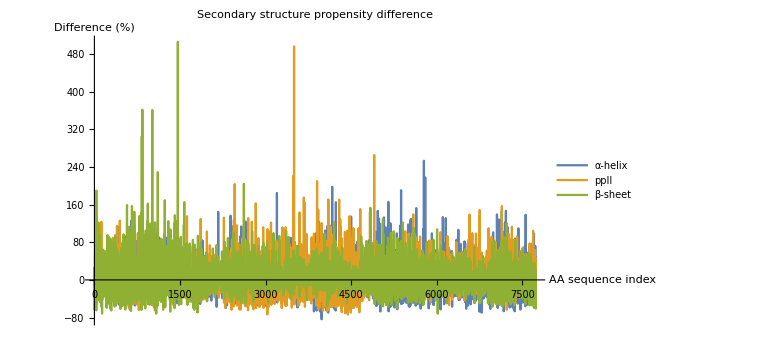

```mathematica
old`prob=Partition[Import["/Volumes/WDBlue/!Advanced_Machine_Learning/Final_project/CA_NN_2/CA_NN.prob"][[All,-1]],3];
new`prob=Partition[Import["/Volumes/WDBlue/!Advanced_Machine_Learning/Final_project/CA_NN_test/CA_NN.prob"][[All,-1]],3];
diff=(new`prob-old`prob)/old`prob
ListLinePlot[Transpose[diff*100],PlotRange->All,PlotStyle->Normal,TicksStyle->Directive[Black,16],LabelStyle->Directive[Black,16],PlotLegends->{"α-helix","ppII","β-sheet"},PlotLabel->"Secondary structure propensity difference",AxesLabel->{"AA sequence index","Difference (%)"},PlotRange->{{0,9001},{Automatic}},ImageSize->Large]
```

```mathematica
Length[old`prob]
```

7733

## Plot potential functions

```mathematica
CA`NN`info=StringSplit/@Import["/Volumes/WDBlue/!Advanced_Machine_Learning/Final_project/CA_NN_test/CA_NN.info","List"][[2;;]]
```

{{A,5.32,5.58,6.20,6.75,6.90,7.27},{C,5.32,5.62,6.15,6.70,6.85,7.27},{D,5.32,5.65,6.10,6.75,6.90,7.27},{E,5.32,5.58,6.18,6.70,6.85,7.22},{F,5.32,5.68,6.18,6.70,6.85,7.24},{G,5.34,5.78,6.50,7.34},{H,5.32,5.68,6.15,6.70,6.85,7.26},{I,5.32,5.58,6.16,6.70,6.85,7.20},{K,5.32,5.60,6.16,6.70,6.85,7.20},{L,5.32,5.60,6.16,6.70,6.85,7.16},{M,5.32,5.56,6.18,6.70,6.85,7.27},{N,5.32,5.70,6.10,6.75,6.85,7.26},{P,5.30,5.64,6.20,6.70},{Q,5.32,5.62,6.18,6.70,6.85,7.24},{R,5.32,5.60,6.16,6.70,6.85,7.24},{S,5.32,5.62,6.30,6.76,6.90,7.27},{T,5.32,5.62,6.30,6.76,6.90,7.26},{V,5.32,5.58,6.18,6.70,6.85,7.20},{W,5.32,5.62,6.18,6.80,6.85,7.24},{Y,5.32,5.64,6.18,6.80,6.85,7.26}}

```mathematica
delE[p_]:=Log[p]
potWell[lower_,upper_,prob_]:=Piecewise[{(*{0,x<=lower},*){delE[prob],lower<=x≤upper}(*,{0,x>=upper}*)}]
```

```mathematica
Show[Plot[{potWell[5.32,5.68,.410],potWell[6.18,6.7,.295],potWell[6.85,7.24,.295]},{x,5,7.5},PlotRange->{Automatic,{-0.01,-2}},PlotStyle->Red,,PlotLegends->{"New"}],
Plot[{potWell[5.32,5.68,.495],potWell[6.18,6.7,.230],potWell[6.85,7.24,.275]},{x,5,7.5},PlotRange->{Automatic,{-0.01,-2}},PlotStyle->Blue,,PlotLegends->{"Old"}],LabelStyle->Medium,LabelStyle->Directive@Black,AxesLabel->{"Distance (Å)","∆E (kT)"},AxesOrigin->{5,-2},TicksStyle->Black]
```

Plot::nonopt: Options expected (instead of Null) beyond position 2 in Plot[{potWell[5.32,5.68,0.41],potWell[6.18,6.7,0.295],potWell[6.85,7.24,0.295]},{x,5,7.5},PlotRange→{Automatic,{-0.01,-2}},PlotStyle→Red,Null,PlotLegends→{New}]. An option must be a rule or a list of rules.

Plot::nonopt: Options expected (instead of Null) beyond position 2 in Plot[{potWell[5.32,5.68,0.495],potWell[6.18,6.7,0.23],potWell[6.85,7.24,0.275]},{x,5,7.5},PlotRange→{Automatic,{-0.01,-2}},PlotStyle→Blue,Null,PlotLegends→{Old}]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{potWell[5.32,5.68,0.41],potWell[6.18,6.7,0.295],potWell[6.85,7.24,0.295]},{x,5,7.5},PlotRange→{Automatic,{-0.01,-2}},PlotStyle→Red,Null,PlotLegends→{New}],«5»,TicksStyle→GrayLevel[0]].

Show[Plot[{potWell[5.32,5.68,0.41],potWell[6.18,6.7,0.295],potWell[6.85,7.24,0.295]},{x,5,7.5},PlotRange→{Automatic,{-0.01,-2}},PlotStyle→Red,Null,PlotLegends→{New}],Plot[{potWell[5.32,5.68,0.495],potWell[6.18,6.7,0.23],potWell[6.85,7.24,0.275]},{x,5,7.5},PlotRange→{Automatic,{-0.01,-2}},PlotStyle→Blue,Null,PlotLegends→{Old}],LabelStyle→Medium,LabelStyle→Directive[GrayLevel[0]],AxesLabel→{Distance (Å),∆E (kT)},AxesOrigin→{5,-2},TicksStyle→GrayLevel[0]]

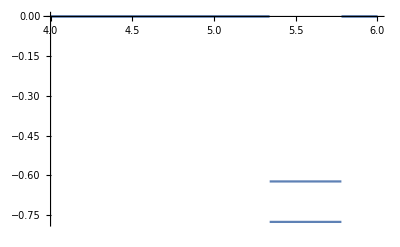

```mathematica
(*WGR, alpha*)
Show[potWell[5.34,5.78,.46],potWell[5.34,5.78,.536],Style->{Blue,Red}]
```

```mathematica
delE[.562]
delE[.444]
```

0.576253

0.811931